```mathematica
PathPoly[n_]:=PathPoly[n]=ChromaticPolynomial[PathGraph[Range[n]],x]
```

```mathematica
PathBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = PathPoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
PathBaseCoeff[Chromial[10]]
```

{0,0,32,-112,160,-120,50,-11,1}

```mathematica
CycleBaseCoeff[Chromial[10]]
```

{0,0,-80,48,40,-70,39,-10,1}

```mathematica
PathGraph[10]
```

PathGraph[10]

```mathematica
Clear[PathPoly]
```

```mathematica
CacheProblem2[n_]:=CacheProblem2[n]=With[
{P=Chromial[n]},
Problem[CoefficientList[P,x],JacobsthalBaseCoeff[P]]
]
```

```mathematica
DeleteDuplicates[
Monitor[
Table[
CacheProblem[k],{k,1000,1010}]
,k]
]
```

```mathematica
14^2
```

196

```mathematica
167
```

```mathematica
183
```

```mathematica
211
```

```mathematica
308
```

```mathematica
JacobsthalBaseCoeff[Chromial[9151]]
```

{0,0,0,-165,-808,-1338,49,464,144,-33,-28,-4,0,1}

```mathematica
Chromial[9151]
```

186138 x-852849 x^2+1752462 x^3-2148156 x^4+1757265 x^5-1014217 x^6+424732 x^7-130367 x^8+29172 x^9-4650 x^10+502 x^11-33 x^12+x^13

```mathematica
boega=With[{size=15},

Flatten[
Matt[size]/.Solve[x2m3==0&&
(*

x12m13==30&&
x11m13==395&&
x2m13==-2046&&
x3m13==2047&&*)

DiagConstr[size]&&
LowerHalfIs[size,0]&&
(*DeterminateConstraint[size]&&*)
BaseConstr[size]&&
Fold[And,
With[
{aaa=DeleteDuplicates[
Monitor[
Table[
CacheProblem2[k],{k,1,100000(*58716*)}]
,k]
]},
Print[Length[aaa]];aaa
]
]
,
Vars[size]
],1]
];MatrixForm[boega]
```

907

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -2 | -6 | -14 | -30 | -62 | -126 | -254 | -510 | -1022 | -2046 | -4094 | -8190
0 | 0 | 1 | 3 | 7 | 15 | 31 | 63 | 127 | 255 | 511 | 1023 | 2047 | 4095 | 8191
0 | 0 | 0 | 1 | 6 | 25 | 89 | 286 | 836 | 2185 | 4923 | 9214 | 16892 | 66595 | 438491
0 | 0 | 0 | 0 | 1 | 9 | 50 | 215 | 760 | 2198 | 4826 | 6012 | -2885 | 11968 | 540477
0 | 0 | 0 | 0 | 0 | 1 | 12 | 85 | 453 | 1953 | 6862 | 18573 | 30491 | -16027 | -185140
0 | 0 | 0 | 0 | 0 | 0 | 1 | 15 | 129 | 819 | 4162 | 17217 | 55733 | 118316 | 4712
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 18 | 182 | 1340 | 7836 | 37276 | 140470 | 367546
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 21 | 244 | 2043 | 13505 | 72578 | 311831
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 24 | 315 | 2955 | 21780 | 130431
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 27 | 395 | 4103 | 33353
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 30 | 484 | 5514
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 33 | 582
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 36
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[Inverse[boega]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 2 | -6 | 18 | -64 | 210 | -664 | 2058 | -6304 | 19170 | -58024 | 175098 | -527344
0 | 0 | 1 | -3 | 11 | -39 | 154 | -565 | 1992 | -6839 | 23030 | -76425 | 250756 | -815419 | 2632626
0 | 0 | 0 | 1 | -6 | 29 | -137 | 594 | -2432 | 9533 | -36115 | 133172 | -480554 | 1703943 | -5955413
0 | 0 | 0 | 0 | 1 | -9 | 58 | -320 | 1595 | -7378 | 32228 | -134592 | 542325 | -2122890 | 8114854
0 | 0 | 0 | 0 | 0 | 1 | -12 | 95 | -615 | 3500 | -18158 | 87822 | -402090 | 1762035 | -7451235
0 | 0 | 0 | 0 | 0 | 0 | 1 | -15 | 141 | -1050 | 6734 | -38808 | 206262 | -1028940 | 4878423
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -18 | 196 | -1652 | 11802 | -74886 | 434280 | -2346564
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -21 | 260 | -2448 | 19290 | -133716 | 840708
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -24 | 333 | -3465 | 29865 | -224631
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -27 | 415 | -4730 | 44275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -30 | 506 | -6270
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -33 | 606
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -36
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
fff=-{{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, -1, -5, -13, -29, -61, -125, -253, -509, -1021, -2045}, {0, 2, 1, -1, -5, -1310,4, -29, -61, -125, -253, -509, -1021}, {0, 4, -1, -10, -25, -46, -62, -25, 205, 914, 2372, 4103}, {0, 8, 1, -13, -40, -88, -159, -218, -121, 421, 1257, -1141}, {0, 16, -1, -35, -103, -238, -499, -970, -1690, -2366, -1809, 1198}, {0, 32, 1, -61, -185, -433, -928, -1906, -3776, -7054, -11647, -14464}, {0, 64, -1, -131, -391, -911, -1951, -4030, -8173, -16329, -31811, -58595}, {0, 128, 1, -253, -761, -1777, -3809, -7873, -16000, -32236, -64525, -127750}, {0, 256, -1, -515, -1543, -3599, -7711, -15935, -32383, -65278, -131047, -262340}, {0, 512, 1, -1021, -3065, -7153, -15329, -31681, -64385, -129793, -260608, -522214}, {0, 1024, -1, -2051, -6151, -14351, -30751, -63551, -129151, -260351, -522751, -1047550}}
```

```mathematica
NSolve[(4923+x)*2-1==9214]
```

{{x→-315.5}}

```mathematica
NSolve[(2185+x)*2-1==4923]
```

{{x→277.}}

```mathematica
NSolve[(2185+x)*2==4923]
```

{{x→276.5}}

```mathematica
NSolve[-490841+33 x  ==9214,x]
```

{{x→15153.2}}

```mathematica
Select[Table[{x,-490841+33 x},{x,15153,16000}],9214<#[[2]]<2*9214&]
```

{{15154,9241},{15155,9274},{15156,9307},{15157,9340},{15158,9373},{15159,9406},{15160,9439},{15161,9472},{15162,9505},{15163,9538},{15164,9571},{15165,9604},{15166,9637},{15167,9670},{15168,9703},{15169,9736},{15170,9769},{15171,9802},{15172,9835},{15173,9868},{15174,9901},{15175,9934},{15176,9967},{15177,10000},{15178,10033},{15179,10066},{15180,10099},{15181,10132},{15182,10165},{15183,10198},{15184,10231},{15185,10264},{15186,10297},{15187,10330},{15188,10363},{15189,10396},{15190,10429},{15191,10462},{15192,10495},{15193,10528},{15194,10561},{15195,10594},{15196,10627},{15197,10660},{15198,10693},{15199,10726},{15200,10759},{15201,10792},{15202,10825},{15203,10858},{15204,10891},{15205,10924},{15206,10957},{15207,10990},{15208,11023},{15209,11056},{15210,11089},{15211,11122},{15212,11155},{15213,11188},{15214,11221},{15215,11254},{15216,11287},{15217,11320},{15218,11353},{15219,11386},{15220,11419},{15221,11452},{15222,11485},{15223,11518},{15224,11551},{15225,11584},{15226,11617},{15227,11650},{15228,11683},{15229,11716},{15230,11749},{15231,11782},{15232,11815},{15233,11848},{15234,11881},{15235,11914},{15236,11947},{15237,11980},{15238,12013},{15239,12046},{15240,12079},{15241,12112},{15242,12145},{15243,12178},{15244,12211},{15245,12244},{15246,12277},{15247,12310},{15248,12343},{15249,12376},{15250,12409},{15251,12442},{15252,12475},{15253,12508},{15254,12541},{15255,12574},{15256,12607},{15257,12640},{15258,12673},{15259,12706},{15260,12739},{15261,12772},{15262,12805},{15263,12838},{15264,12871},{15265,12904},{15266,12937},{15267,12970},{15268,13003},{15269,13036},{15270,13069},{15271,13102},{15272,13135},{15273,13168},{15274,13201},{15275,13234},{15276,13267},{15277,13300},{15278,13333},{15279,13366},{15280,13399},{15281,13432},{15282,13465},{15283,13498},{15284,13531},{15285,13564},{15286,13597},{15287,13630},{15288,13663},{15289,13696},{15290,13729},{15291,13762},{15292,13795},{15293,13828},{15294,13861},{15295,13894},{15296,13927},{15297,13960},{15298,13993},{15299,14026},{15300,14059},{15301,14092},{15302,14125},{15303,14158},{15304,14191},{15305,14224},{15306,14257},{15307,14290},{15308,14323},{15309,14356},{15310,14389},{15311,14422},{15312,14455},{15313,14488},{15314,14521},{15315,14554},{15316,14587},{15317,14620},{15318,14653},{15319,14686},{15320,14719},{15321,14752},{15322,14785},{15323,14818},{15324,14851},{15325,14884},{15326,14917},{15327,14950},{15328,14983},{15329,15016},{15330,15049},{15331,15082},{15332,15115},{15333,15148},{15334,15181},{15335,15214},{15336,15247},{15337,15280},{15338,15313},{15339,15346},{15340,15379},{15341,15412},{15342,15445},{15343,15478},{15344,15511},{15345,15544},{15346,15577},{15347,15610},{15348,15643},{15349,15676},{15350,15709},{15351,15742},{15352,15775},{15353,15808},{15354,15841},{15355,15874},{15356,15907},{15357,15940},{15358,15973},{15359,16006},{15360,16039},{15361,16072},{15362,16105},{15363,16138},{15364,16171},{15365,16204},{15366,16237},{15367,16270},{15368,16303},{15369,16336},{15370,16369},{15371,16402},{15372,16435},{15373,16468},{15374,16501},{15375,16534},{15376,16567},{15377,16600},{15378,16633},{15379,16666},{15380,16699},{15381,16732},{15382,16765},{15383,16798},{15384,16831},{15385,16864},{15386,16897},{15387,16930},{15388,16963},{15389,16996},{15390,17029},{15391,17062},{15392,17095},{15393,17128},{15394,17161},{15395,17194},{15396,17227},{15397,17260},{15398,17293},{15399,17326},{15400,17359},{15401,17392},{15402,17425},{15403,17458},{15404,17491},{15405,17524},{15406,17557},{15407,17590},{15408,17623},{15409,17656},{15410,17689},{15411,17722},{15412,17755},{15413,17788},{15414,17821},{15415,17854},{15416,17887},{15417,17920},{15418,17953},{15419,17986},{15420,18019},{15421,18052},{15422,18085},{15423,18118},{15424,18151},{15425,18184},{15426,18217},{15427,18250},{15428,18283},{15429,18316},{15430,18349},{15431,18382},{15432,18415}}

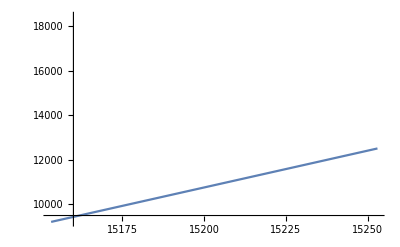

```mathematica
Plot[-490841+33 x,{x,15153,15153+100},PlotRange->{Automatic,{9214,18428}}]
```

```mathematica
Solve[Det[{{a,b},{c,d}}]==23,{a,b,c,d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{d→(23+b c)/a},{a→0,c→-23/b}}

```mathematica
MatrixForm[Inverse[fff]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -16912919/3 | -16827431/3 | 2 | -6 | 18 | -64 | 210 | -664 | 2058 | -6304 | 19170
0 | 68213542/3 | 67886371/3 | -3 | 11 | -39 | 154 | -565 | 1992 | -6839 | 23030 | -76425
0 | -40134830 | -39952811 | 1 | -6 | 29 | -137 | 594 | -2432 | 9533 | -36115 | 133172
0 | 41125734 | 40949553 | 0 | 1 | -9 | 58 | -320 | 1595 | -7378 | 32228 | -134592
0 | -27225410 | -27115207 | 0 | 0 | 1 | -12 | 95 | -615 | 3500 | -18158 | 87822
0 | 12212254 | 12165505 | 0 | 0 | 0 | 1 | -15 | 141 | -1050 | 6734 | -38808
0 | -3771566 | -3757897 | 0 | 0 | 0 | 0 | 1 | -18 | 196 | -1652 | 11802
0 | 794780 | 792050 | 0 | 0 | 0 | 0 | 0 | 1 | -21 | 260 | -2448
0 | -109892 | -109534 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -24 | 333
0 | 9064 | 9036 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -27
0 | -342 | -341 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
FindGeneratingFunction[{10,40,238,928,4030,16000,65278,260608,1047550},x]
```

```mathematica
FindGeneratingFunction[{1,6,25,89,286,836,2185,4923,9214},x]
```

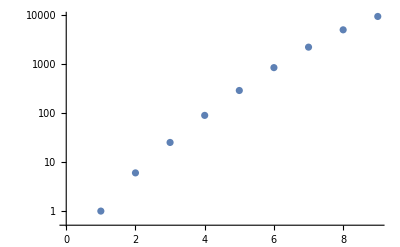

```mathematica
ListLogPlot[{1,6,25,89,286,836,2185,4923,9214}]
```

```mathematica
Table[14.2931 E^(0.720294 x),{x,Range[10]}]
```

{29.3729,60.3623,124.047,254.921,523.872,1076.58,2212.4,4546.57,9343.38,19201.}

```mathematica
six={{{1,2}},{{1,2},{1,3}},{{3,6},{4,5}},{{1,2},{1,3},{1,4}},{{4,5},{4,6},{5,6}},{{3,6},{4,5},{5,6}},{{2,6},{3,6},{4,5}},{{1,6},{2,5},{3,4}},{{1,2},{1,3},{1,4},{1,5}},{{3,6},{4,5},{4,6},{5,6}},{{3,5},{3,6},{4,5},{4,6}},{{2,6},{3,6},{4,5},{5,6}},{{2,6},{3,5},{4,5},{4,6}},{{2,6},{3,4},{3,5},{4,5}},{{1,6},{2,6},{3,6},{4,5}},{{1,6},{2,6},{3,5},{4,5}},{{1,6},{2,5},{3,4},{5,6}},{{1,2},{1,3},{1,4},{1,5},{1,6}},{{3,5},{3,6},{4,5},{4,6},{5,6}},{{2,6},{3,6},{4,5},{4,6},{5,6}},{{2,6},{3,5},{4,5},{4,6},{5,6}},{{2,6},{3,5},{3,6},{4,5},{4,6}},{{2,6},{3,4},{3,5},{4,5},{5,6}},{{2,5},{2,6},{3,4},{3,6},{4,5}},{{1,6},{2,6},{3,6},{4,5},{5,6}},{{1,6},{2,6},{3,5},{4,5},{5,6}},{{1,6},{2,6},{3,5},{4,5},{4,6}},{{1,6},{2,6},{3,4},{3,5},{4,5}},{{1,6},{2,5},{3,4},{4,6},{5,6}},{{1,6},{2,5},{3,4},{3,6},{4,6}},{{1,6},{2,5},{3,4},{3,6},{4,5}},{{1,6},{2,4},{2,5},{3,4},{3,5}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3}},{{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{2,6},{3,5},{3,6},{4,5},{4,6},{5,6}},{{2,6},{3,4},{3,5},{4,5},{4,6},{5,6}},{{2,5},{2,6},{3,5},{3,6},{4,5},{4,6}},{{2,5},{2,6},{3,4},{3,6},{4,6},{5,6}},{{2,5},{2,6},{3,4},{3,6},{4,5},{5,6}},{{1,6},{2,6},{3,5},{4,5},{4,6},{5,6}},{{1,6},{2,6},{3,5},{3,6},{4,5},{4,6}},{{1,6},{2,6},{3,4},{3,5},{4,5},{5,6}},{{1,6},{2,5},{3,5},{3,6},{4,5},{4,6}},{{1,6},{2,5},{3,4},{4,5},{4,6},{5,6}},{{1,6},{2,5},{3,4},{3,6},{4,6},{5,6}},{{1,6},{2,5},{3,4},{3,6},{4,5},{5,6}},{{1,6},{2,5},{3,4},{3,6},{4,5},{4,6}},{{1,6},{2,5},{2,6},{3,4},{3,6},{4,5}},{{1,6},{2,5},{2,6},{3,4},{3,5},{4,5}},{{1,6},{2,4},{2,5},{3,4},{3,5},{5,6}},{{1,6},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,5},{1,6},{2,4},{2,6},{3,4},{3,5}},{{1,5},{1,6},{2,3},{2,4},{3,4},{5,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4}},{{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{2,5},{2,6},{3,5},{3,6},{4,5},{4,6},{5,6}},{{2,5},{2,6},{3,4},{3,6},{4,5},{4,6},{5,6}},{{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6}},{{1,6},{2,6},{3,4},{3,5},{4,5},{4,6},{5,6}},{{1,6},{2,5},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,6},{2,5},{3,4},{3,6},{4,5},{4,6},{5,6}},{{1,6},{2,5},{3,4},{3,5},{3,6},{4,5},{4,6}},{{1,6},{2,5},{2,6},{3,5},{3,6},{4,5},{4,6}},{{1,6},{2,5},{2,6},{3,4},{3,6},{4,6},{5,6}},{{1,6},{2,5},{2,6},{3,4},{3,6},{4,5},{5,6}},{{1,6},{2,5},{2,6},{3,4},{3,5},{4,5},{5,6}},{{1,6},{2,5},{2,6},{3,4},{3,5},{4,5},{4,6}},{{1,6},{2,4},{2,5},{3,4},{3,5},{4,6},{5,6}},{{1,6},{2,4},{2,5},{3,4},{3,5},{4,5},{5,6}},{{1,6},{2,4},{2,5},{3,4},{3,5},{3,6},{5,6}},{{1,6},{2,4},{2,5},{3,4},{3,5},{3,6},{4,5}},{{1,6},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},{{1,5},{1,6},{2,5},{2,6},{3,4},{3,6},{4,6}},{{1,5},{1,6},{2,5},{2,6},{3,4},{3,6},{4,5}},{{1,5},{1,6},{2,4},{2,6},{3,4},{3,5},{5,6}},{{1,5},{1,6},{2,4},{2,6},{3,4},{3,5},{3,6}},{{1,5},{1,6},{2,3},{2,4},{3,4},{4,6},{5,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5}},{{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,6},{5,6}},{{1,6},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,6},{2,5},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,6},{2,5},{2,6},{3,4},{3,6},{4,5},{4,6},{5,6}},{{1,6},{2,5},{2,6},{3,4},{3,5},{4,5},{4,6},{5,6}},{{1,6},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6}},{{1,6},{2,4},{2,5},{3,4},{3,5},{4,5},{4,6},{5,6}},{{1,6},{2,4},{2,5},{3,4},{3,5},{3,6},{4,6},{5,6}},{{1,6},{2,4},{2,5},{3,4},{3,5},{3,6},{4,5},{5,6}},{{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5}},{{1,6},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5},{5,6}},{{1,5},{1,6},{2,5},{2,6},{3,5},{3,6},{4,5},{4,6}},{{1,5},{1,6},{2,5},{2,6},{3,4},{3,6},{4,6},{5,6}},{{1,5},{1,6},{2,5},{2,6},{3,4},{3,6},{4,5},{5,6}},{{1,5},{1,6},{2,5},{2,6},{3,4},{3,6},{4,5},{4,6}},{{1,5},{1,6},{2,4},{2,6},{3,4},{3,5},{4,6},{5,6}},{{1,5},{1,6},{2,4},{2,6},{3,4},{3,5},{3,6},{5,6}},{{1,5},{1,6},{2,4},{2,6},{3,4},{3,5},{3,6},{4,5}},{{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6}},{{1,5},{1,6},{2,3},{2,4},{3,4},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,3},{2,4},{3,4},{3,6},{4,5},{5,6}},{{1,5},{1,6},{2,3},{2,4},{2,6},{3,4},{3,6},{4,5}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6}},{{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,6},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,6},{2,4},{2,5},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,6},{5,6}},{{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{5,6}},{{1,6},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,5},{2,6},{3,4},{3,6},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6}},{{1,5},{1,6},{2,4},{2,6},{3,4},{3,5},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,4},{2,6},{3,4},{3,5},{3,6},{4,6},{5,6}},{{1,5},{1,6},{2,4},{2,6},{3,4},{3,5},{3,6},{4,5},{5,6}},{{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{5,6}},{{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,6}},{{1,5},{1,6},{2,3},{2,4},{3,4},{3,6},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,3},{2,4},{2,6},{3,4},{3,6},{4,6},{5,6}},{{1,5},{1,6},{2,3},{2,4},{2,6},{3,4},{3,6},{4,5},{5,6}},{{1,5},{1,6},{2,3},{2,4},{2,6},{3,4},{3,6},{4,5},{4,6}},{{1,5},{1,6},{2,3},{2,4},{2,6},{3,4},{3,5},{4,5},{4,6}},{{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6}},{{1,4},{1,5},{1,6},{2,3},{2,5},{2,6},{3,4},{3,6},{4,5}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4}},{{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,6},{2,3},{2,4},{2,5},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,4},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,6},{5,6}},{{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6}},{{1,5},{1,6},{2,3},{2,4},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,3},{2,4},{2,6},{3,4},{3,6},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,3},{2,4},{2,6},{3,4},{3,5},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,3},{2,4},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6}},{{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{5,6}},{{1,4},{1,5},{1,6},{2,3},{2,5},{2,6},{3,5},{3,6},{4,5},{4,6}},{{1,4},{1,5},{1,6},{2,3},{2,5},{2,6},{3,4},{3,6},{4,6},{5,6}},{{1,4},{1,5},{1,6},{2,3},{2,5},{2,6},{3,4},{3,6},{4,5},{5,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5}},{{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,3},{2,4},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6}},{{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,6},{5,6}},{{1,4},{1,5},{1,6},{2,3},{2,5},{2,6},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,4},{1,5},{1,6},{2,3},{2,5},{2,6},{3,4},{3,6},{4,5},{4,6},{5,6}},{{1,4},{1,5},{1,6},{2,3},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6}},{{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{5,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6}},{{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,4},{1,5},{1,6},{2,3},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,6},{5,6}},{{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,5},{3,6},{4,5},{4,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5}},{{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,5},{3,6},{4,5},{4,6},{5,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}};Length[six]
```

155

```mathematica
Map[ChromaticPolynomial[Graph[#],4]/24&,six]//Tally//Sort
```

{{0,6},{1/2,1},{1,3},{3/2,1},{2,4},{3,4},{4,7},{9/2,1},{5,4},{6,6},{7,2},{8,8},{9,7},{10,3},{11,1},{12,11},{13,2},{27/2,1},{14,4},{15,3},{16,4},{17,1},{35/2,1},{18,10},{20,2},{41/2,1},{21,4},{43/2,1},{23,1},{24,5},{49/2,1},{51/2,2},{27,7},{28,1},{30,1},{61/2,1},{63/2,4},{32,1},{34,1},{36,5},{40,1},{81/2,6},{42,2},{48,2},{54,5},{56,1},{64,1},{72,3},{96,1}}

```mathematica
Map[Graph[#, VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]&,Select[six,PlanarGraphQ[#]&]]
```

{}

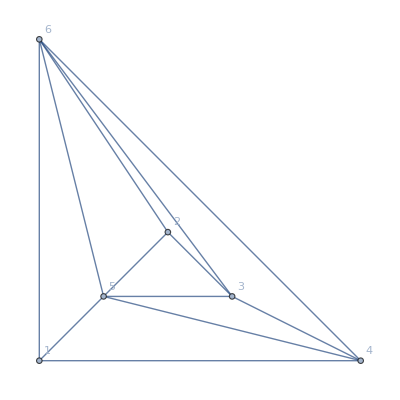
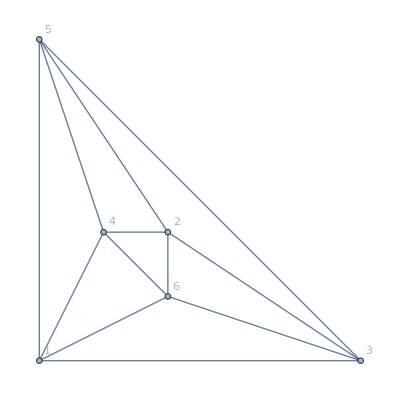
{{24,-Graphics-},{96,-Graphics-}}

```mathematica
Map[{ChromaticPolynomial[Graph[#],4],Graph[#, VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]}&,Select[six,
With[{g=Graph[#]},
VertexCount[g]==6&&PlanarGraphQ[g] && MaximalPlanarQ[g]
]&]]//Sort
```

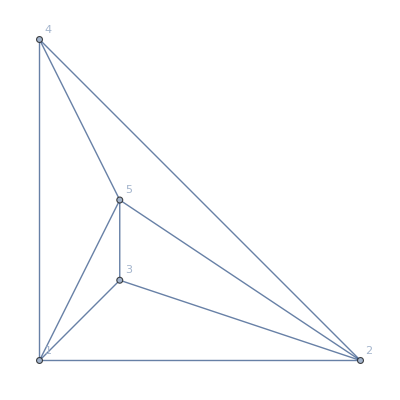

```mathematica
Graph[JacobsThalGraph[1], VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

```mathematica
four={{{1,2}},{{1,2},{1,3}},{{1,4},{2,3}},{{1,2},{1,3},{1,4}},{{2,3},{2,4},{3,4}},{{1,4},{2,3},{3,4}},{{1,2},{1,3},{1,4},{2,3}},{{1,3},{1,4},{2,3},{2,4}},{{1,2},{1,3},{1,4},{2,3},{2,4}},{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}}
```

{{{1,2}},{{1,2},{1,3}},{{1,4},{2,3}},{{1,2},{1,3},{1,4}},{{2,3},{2,4},{3,4}},{{1,4},{2,3},{3,4}},{{1,2},{1,3},{1,4},{2,3}},{{1,3},{1,4},{2,3},{2,4}},{{1,2},{1,3},{1,4},{2,3},{2,4}},{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}}

```mathematica
TableForm[
Table[
ChromaticPolynomial[JacobsThalGraph[k],x],{k,1,5}]
]
```

18 x-39 x^2+29 x^3-9 x^4+x^5
-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6
210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7
-664 x+1992 x^2-2432 x^3+1595 x^4-615 x^5+141 x^6-18 x^7+x^8
2058 x-6839 x^2+9533 x^3-7378 x^4+3500 x^5-1050 x^6+196 x^7-21 x^8+x^9

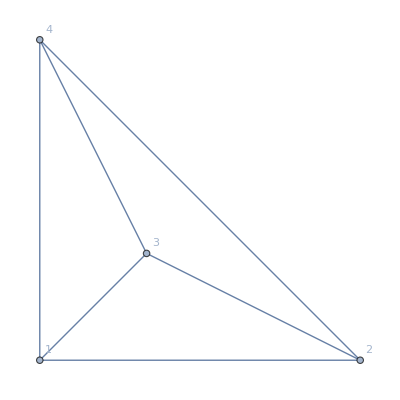
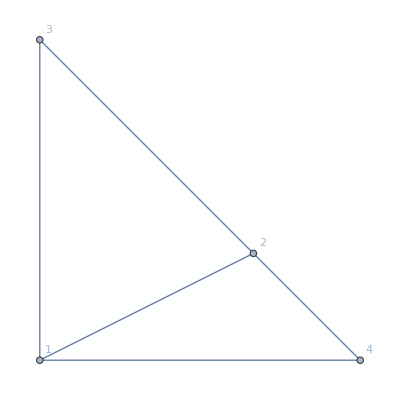
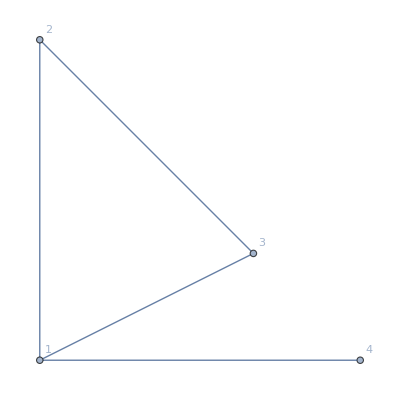
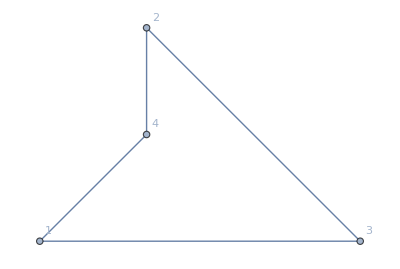
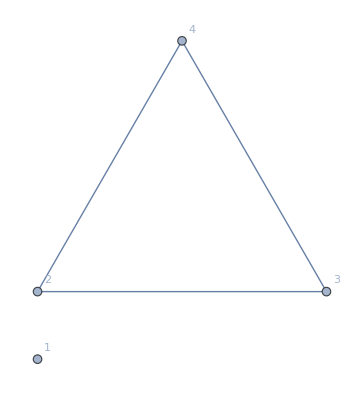
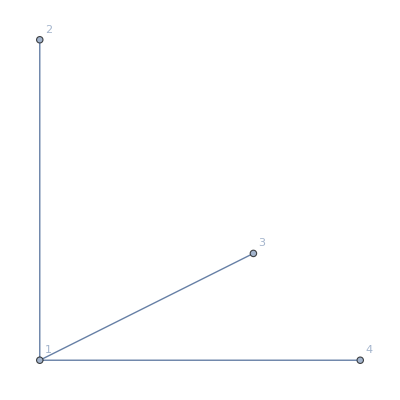
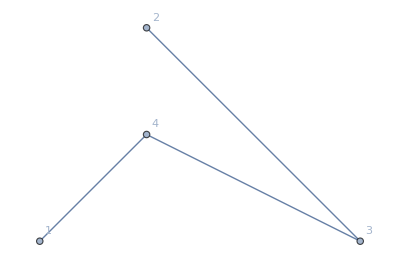
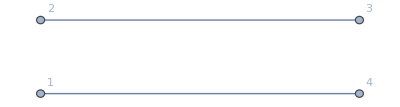
{{-6 x+11 x^2-6 x^3+x^4,-Graphics-},{-4 x+8 x^2-5 x^3+x^4,-Graphics-},{-2 x+5 x^2-4 x^3+x^4,-Graphics-},{-3 x+6 x^2-4 x^3+x^4,-Graphics-},{2 x^2-3 x^3+x^4,-Graphics-},{-x+3 x^2-3 x^3+x^4,-Graphics-},{-x+3 x^2-3 x^3+x^4,-Graphics-},{x^2-2 x^3+x^4,-Graphics-}}

```mathematica
Map[{ChromaticPolynomial[Graph[#],x],Graph[#, VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]}&,Select[four,
With[{g=Graph[#]},
VertexCount[g]==4&&PlanarGraphQ[g] 
]&]]//Sort
```

```mathematica
drie={{{1,2}},{{1,2},{1,3}},{{1,2},{1,3},{2,3}}}
```

{{{1,2}},{{1,2},{1,3}},{{1,2},{1,3},{2,3}}}